```mathematica
Range[0,10,.5]//Length
```

21

```mathematica
t0=AbsoluteTime[{1970,1,1}];
```

```mathematica
d=Import[FileNameJoin[{NotebookDirectory[],"..","build","SW_EFIB_image_stats_timeseries.txt"}],"Table"]/.{t_?NumberQ,rest__}:>{t+t0,rest};
```

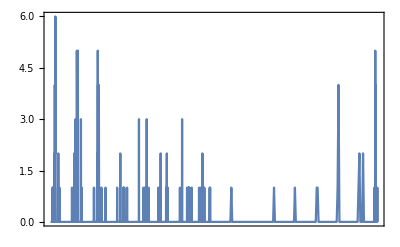

```mathematica
DateListPlot[d[[All,{1,2}]]]
```

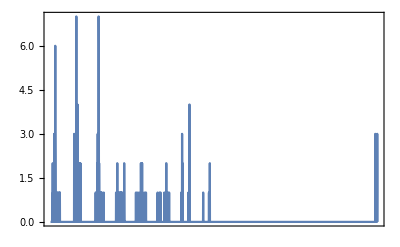

```mathematica
DateListPlot[d[[All,{1,3}]]]
```

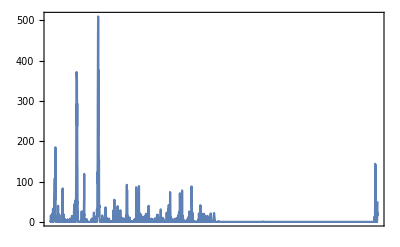

```mathematica
DateListPlot[d[[All,{1,4}]],PlotRange->All]
```

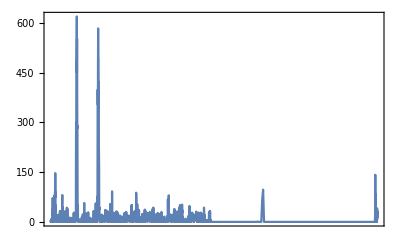

```mathematica
DateListPlot[d[[All,{1,5}]],PlotRange->All]
```

```mathematica
DateListPlot[d[[All,{1,5}]],PlotRange->All]
```

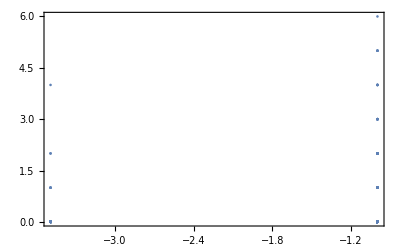

```mathematica
ListPlot[d[[All,{-1,2}]],Frame->True,PlotRange->All]
```

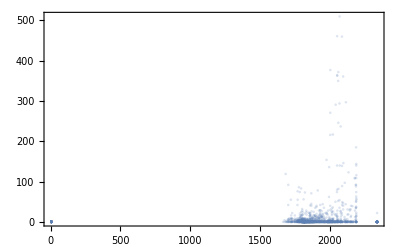

```mathematica
ListPlot[d[[All,{8,4}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```

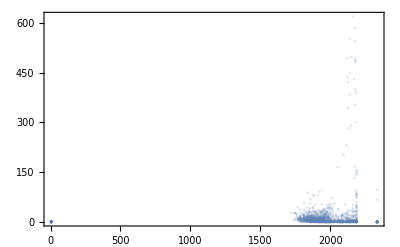

```mathematica
ListPlot[d[[All,{9,5}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```

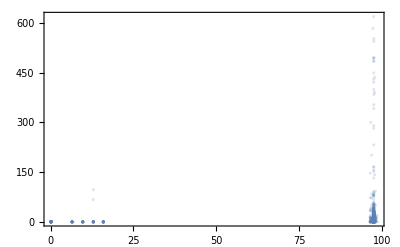

```mathematica
ListPlot[d[[All,{11,5}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```

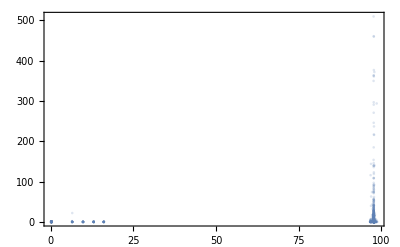

```mathematica
ListPlot[d[[All,{10,4}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```